```mathematica
Series[Cos[x],{0,2}]
```

Series::sspec: Series specification {0,2} is not a list with three elements.

```mathematica
Series[Cos[x],{x,0,5}]
```

1-x^2/2+x^4/24+O[x]^6

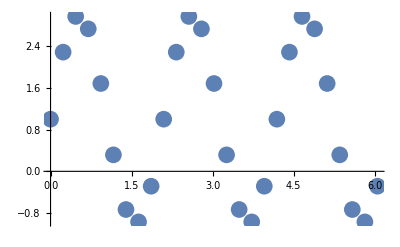

```mathematica
fig0=ListPlot[Partition[Flatten[Import["/home/andrey/CLionProjects/NumericalMethods/Lab10/files/U2.txt","Table"]],2],PlotRange->All,PlotStyle->PointSize[0.03]]
```

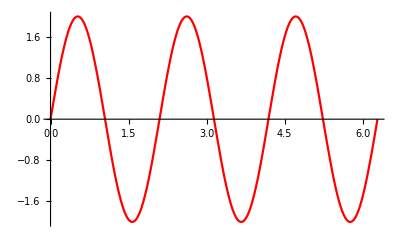

4.17005

```mathematica
fig1 = Plot[2*Sin[3*t],{t,0,2*Pi},PlotStyle->Red]

Log[31/22,28/6.7]
```

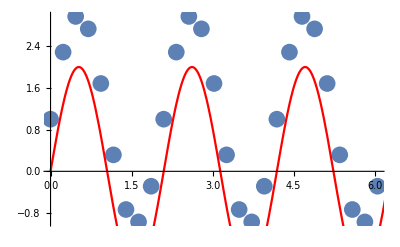

4.17005

```mathematica
Show[fig0,fig1]
```

x-x^3/6+x^5/120-Sin[x]

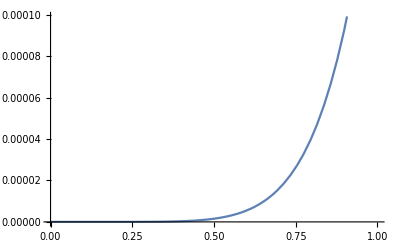

x-x^3/6+x^5/120+Sin[x]

```mathematica
delta[x_]=-Sin[x]+x -x^3/6 + x^5/120
Plot[delta[x],{x,0,1}]
```

```mathematica
normDeltaK = N[delta[1]]
```

0.000195682

0.5 (1+Sin[x])

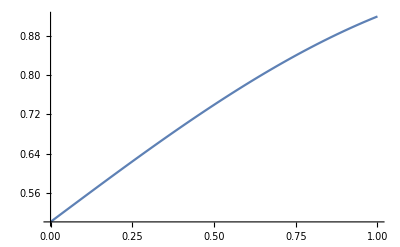

```mathematica
f[x_] = 0.5*(1+Sin[x])
Plot[f[x] ,{x,0,1}]
```

```mathematica
normF = N[f[1]]
```

0.920735

```mathematica
res=normDeltaK * 3 *3 *normF
```

0.00162154

1.

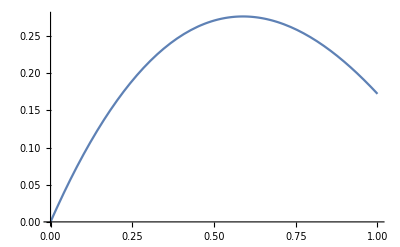

```mathematica
0.0016215410933034442

x=1.0
Plot[x*Cos[x s] - x*Exp[-x s],{s,0,1}]
```

```mathematica
FindMaximum[{In.13tegrate[x*Cos[x s] - x*Exp[-x s],{s,0,1}],0≤x≤1},{x,1}]
```

{0.20935,{1.→0.999999}}

```mathematica
FindMaximum[{Integrate[x^2 s - x^3 s^2+x^4 s^3/6,{s,0,1}],0≤x≤1},{x,1}]
```

{0.208333,{1.→0.999999}}

```mathematica
b = 0.20935
```

0.20935

```mathematica
a = N[5/24]
```

0.208333

```mathematica
Rk1= a/(1-a)
```

0.263158

```mathematica
Rk =b/(1-b)
```

0.264782

```mathematica
deltaK =FindMaximum[{Integrate[x*Cos[x s] - x*Exp[-x s]- x^2 s + x^3 s^2-x^4 s^3/6,{s,0,1}],0≤x≤1},{x,1}]
```

{0.001017,{1.→0.999985}}

```mathematica
normF  = FindMaximum[{2-Exp[-x]-Sin[x],0≤x≤1},{x,1}]
res = deltaK*(1+Rk1)*(1+Rk)
```

{1.,{1.→0.000926695}}

{0.00162478,{1.59762 (1.→0.999985)}}

```mathematica
res
```

{0.00162478,{1.59762 (1.→0.999985)}}